“CityPlot” or “HeatMap” representation of  test matrix used in testme.f90

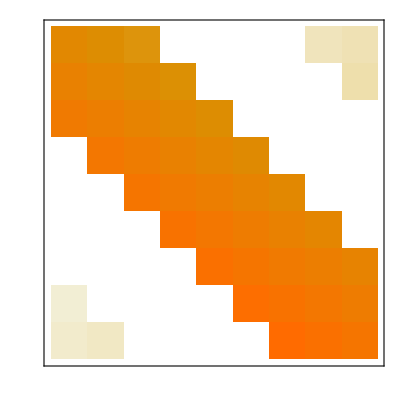

```mathematica
KN=9;
KU=2;
f[i_,j_]:=Block[{ff},
ff=0;
If[Abs[i-j] <= KU,ff=500+3*i-2*j];
If[Abs[i-j] & (i > j)<= KU,ff=501+3*i-2*j];
If[Abs[i - j] ≥ KN-KU,ff=20+i+2*j];
If[Abs[i - j] ≥ KN-KU & (i>j),ff=40+2*i+4*j];
Return[ff]]
MatrixPlot[Array[f,{KN,KN}], FrameTicks->None]
```